## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="RPIb";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_trp2.csv";

mainFolder = "fit_RPIb_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{r5p,Null,Keq substrate}

{0.443,Keq value}

{r5p,Km or S05 substrate}

{0.0011,Km or S05 value}

{{{r5p,Null}},kcat substrates}

{52,kcat value}

(r5p^c⇌ru5p__D^c)^RPIb

Null;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | r5p,Null | 0.443 | 0.42085
0.46515 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | r5p | 0.0011 | 0.0009
0.0013 |  | M | 7.5 | 37 | trishcl | 0.005 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | r5p | Null | 52. | 50.
54. | 1/s | 7.5 | 37 | trishcl | 0.005 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1};
s05Priorities = Null;
kcatPriorities = {1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(r5p^c⇌ru5p__D^c)^RPIb

Null;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | r5p,Null | 0.443 | 0.42085
0.46515 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | r5p | 0.0011 | 0.0009
0.0013 |  | M | 7.5 | 37 | trishcl | 0.005 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | r5p | Null | 52. | 50.
54. | 1/s | 7.5 | 37 | trishcl | 0.005 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_RPIb[c] + r5p[c] <=> E_RPIb[c]&r5p",
				"E_RPIb[c]&r5p <=> E_RPIb[c]&ru5p__D",
				"E_RPIb[c]&ru5p__D <=> E_RPIb[c] + ru5p__D[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((RPIb^c)_^+r5p^c⇌(RPIb^c&r5p^c)_^)^RPIb1,((RPIb^c&ru5p_^D)_^⇌(RPIb^c)_^+ru5p__D^c)^RPIb2,((RPIb^c&r5p^c)_^⇌(RPIb^c&ru5p_^D)_^)^RPIb3}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((RPIb^c)_^+r5p^c⇌(RPIb^c&r5p^c)_^)^RPIb1,Overscript[(RPIb^c&ru5p_^D)_^⇌(RPIb^c)_^+ru5p__D^c, RPIb2],((RPIb^c&r5p^c)_^⇌(RPIb^c&ru5p_^D)_^)^RPIb3};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=2;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

{r5p^c→0}

{ru5p__D^c→0}

{r5p^c→∞}

{ru5p__D^c→∞}

Added inhibition reactions:

{}

Generating flux equation...

{((RPIb^c&r5p^c)_^-((RPIb^c&ru5p_^D)_^)/K_RPIb3) Volume_c k_RPIb3^⟶}

Volume_c (-(RPIb^c&ru5p_^D)_^ k_RPIb3^⟵+(RPIb^c&r5p^c)_^ k_RPIb3^⟶)

1

2

3

0.041747

4

0.00022

5

0.00015

Simplifying...

6

0.04814

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	r5p[c]	ru5p__D[c]	param_RPIb_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt"	0.443
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt"	0.443
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt"	0.443
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt"	0.443
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt"	0.443
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt"	0.443
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt"	0.443
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt"	0.443
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt"	0.443
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt"	0.443
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt"	0.443
1	0.00010999999999999996	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt"	0.09090909090909087
1	0.0001743382511707225	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt"	0.13680688860321003
1	0.00027630750746605366	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt"	0.20076000891310164
1	0.00043791788760884695	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt"	0.2847472489508014
1	0.0006940530789282128	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt"	0.3868631798468571
1	0.0010999999999999996	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt"	0.4999999999999999
1	0.0017433825117072251	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt"	0.6131368201531431
1	0.0027630750746605367	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt"	0.7152527510491985
1	0.004379178876088469	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt"	0.7992399910868981
1	0.006940530789282128	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt"	0.86319311139679
1	0.010999999999999998	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt"	0.9090909090909091
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt"	52.
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt"	52.
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt"	52.
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt"	52.
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt"	52.
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt"	52.
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt"	52.
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt"	52.
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt"	52.
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt"	52.
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt"	52.

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateRev_ru5p__D.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateRev_ru5p__D.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 0.631152669942
best_fit: 0.797921083738
best_fit: 0.815736273653
best_fit: 0.659938632775
best_fit: 1.06841999227

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 3.07038×10^-12 | 9.42722×10^-24 | 3.13194×10^-12 | 7.06984×10^-10 | 0.443 | 0.443
1 | haldaneRatio_1 | 3.07038×10^-12 | 9.42722×10^-24 | 3.13194×10^-12 | 7.06984×10^-10 | 0.443 | 0.443
1 | haldaneRatio_1 | 3.07038×10^-12 | 9.42722×10^-24 | 3.13194×10^-12 | 7.06984×10^-10 | 0.443 | 0.443
1 | haldaneRatio_1 | 3.07038×10^-12 | 9.42722×10^-24 | 3.13194×10^-12 | 7.06984×10^-10 | 0.443 | 0.443
1 | haldaneRatio_1 | 3.07038×10^-12 | 9.42722×10^-24 | 3.13194×10^-12 | 7.06984×10^-10 | 0.443 | 0.443
1 | haldaneRatio_1 | 3.07038×10^-12 | 9.42722×10^-24 | 3.13194×10^-12 | 7.06984×10^-10 | 0.443 | 0.443
1 | haldaneRatio_1 | 3.07038×10^-12 | 9.42722×10^-24 | 3.13194×10^-12 | 7.06984×10^-10 | 0.443 | 0.443
1 | haldaneRatio_1 | 3.07038×10^-12 | 9.42722×10^-24 | 3.13194×10^-12 | 7.06984×10^-10 | 0.443 | 0.443
1 | haldaneRatio_1 | 3.07038×10^-12 | 9.42722×10^-24 | 3.13194×10^-12 | 7.06984×10^-10 | 0.443 | 0.443
1 | haldaneRatio_1 | 3.07038×10^-12 | 9.42722×10^-24 | 3.13194×10^-12 | 7.06984×10^-10 | 0.443 | 0.443
1 | haldaneRatio_1 | 3.07038×10^-12 | 9.42722×10^-24 | 3.13194×10^-12 | 7.06984×10^-10 | 0.443 | 0.443
1 | relRateFor_r5p | 8.47766×10^-13 | 7.18708×10^-25 | 1.77441×10^-13 | 1.95186×10^-10 | 0.0909091 | 0.0909091
1 | relRateFor_r5p | 8.05134×10^-13 | 6.4824×10^-25 | 2.5363×10^-13 | 1.85393×10^-10 | 0.136807 | 0.136807
1 | relRateFor_r5p | 7.45404×10^-13 | 5.55627×10^-25 | 3.44558×10^-13 | 1.71627×10^-10 | 0.20076 | 0.20076
1 | relRateFor_r5p | 6.67022×10^-13 | 4.44918×10^-25 | 4.37317×10^-13 | 1.53581×10^-10 | 0.284747 | 0.284747
1 | relRateFor_r5p | 5.7182×10^-13 | 3.26979×10^-25 | 5.0937×10^-13 | 1.31667×10^-10 | 0.386863 | 0.386863
1 | relRateFor_r5p | 4.66238×10^-13 | 2.17378×10^-25 | 5.36793×10^-13 | 1.07359×10^-10 | 0.5 | 0.5
1 | relRateFor_r5p | 3.60795×10^-13 | 1.30173×10^-25 | 5.0937×10^-13 | 8.30761×10^-11 | 0.613137 | 0.613137
1 | relRateFor_r5p | 2.65538×10^-13 | 7.05102×10^-26 | 4.37317×10^-13 | 6.11416×10^-11 | 0.715253 | 0.715253
1 | relRateFor_r5p | 1.87197×10^-13 | 3.50429×10^-26 | 3.44502×10^-13 | 4.31037×10^-11 | 0.79924 | 0.79924
1 | relRateFor_r5p | 1.27579×10^-13 | 1.62763×10^-26 | 2.53575×10^-13 | 2.93764×10^-11 | 0.863193 | 0.863193
1 | relRateFor_r5p | 8.47517×10^-14 | 7.18284×10^-27 | 1.77414×10^-13 | 1.95155×10^-11 | 0.909091 | 0.909091
1 | absRateFor | 8.83738×10^-13 | 7.80992×10^-25 | 1.05793×10^-10 | 2.03448×10^-10 | 52. | 52.
1 | absRateFor | 8.83738×10^-13 | 7.80992×10^-25 | 1.05793×10^-10 | 2.03448×10^-10 | 52. | 52.
1 | absRateFor | 8.83738×10^-13 | 7.80992×10^-25 | 1.05793×10^-10 | 2.03448×10^-10 | 52. | 52.
1 | absRateFor | 8.83738×10^-13 | 7.80992×10^-25 | 1.05793×10^-10 | 2.03448×10^-10 | 52. | 52.
1 | absRateFor | 8.83738×10^-13 | 7.80992×10^-25 | 1.05793×10^-10 | 2.03448×10^-10 | 52. | 52.
1 | absRateFor | 8.83738×10^-13 | 7.80992×10^-25 | 1.05793×10^-10 | 2.03448×10^-10 | 52. | 52.
1 | absRateFor | 8.83738×10^-13 | 7.80992×10^-25 | 1.05793×10^-10 | 2.03448×10^-10 | 52. | 52.
1 | absRateFor | 8.83738×10^-13 | 7.80992×10^-25 | 1.05793×10^-10 | 2.03448×10^-10 | 52. | 52.
1 | absRateFor | 8.83738×10^-13 | 7.80992×10^-25 | 1.05793×10^-10 | 2.03448×10^-10 | 52. | 52.
1 | absRateFor | 8.83738×10^-13 | 7.80992×10^-25 | 1.05793×10^-10 | 2.03448×10^-10 | 52. | 52.
1 | absRateFor | 8.83738×10^-13 | 7.80992×10^-25 | 1.05793×10^-10 | 2.03448×10^-10 | 52. | 52.

### Simulated Data and Best Fit Data Plot

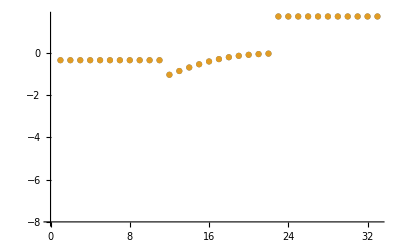

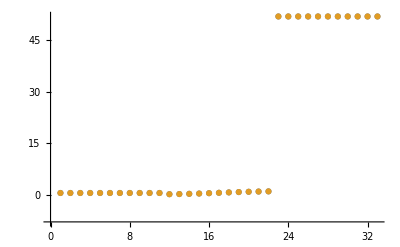

```mathematica
dataSetI=5;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

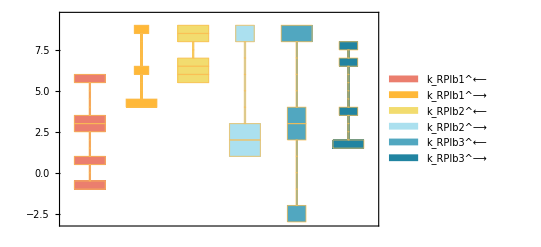

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

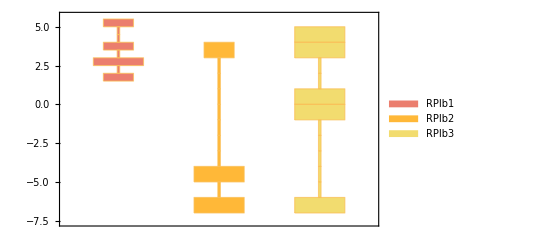

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

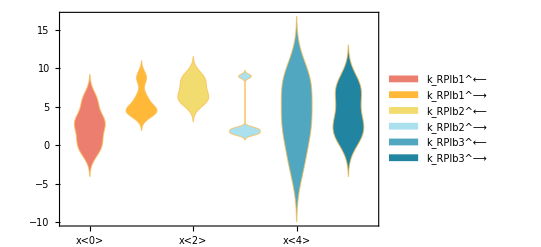

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

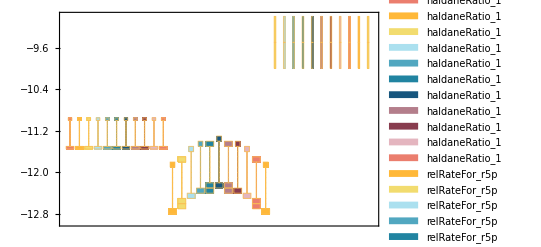

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

backCalculateKms[(r5p^c⇌ru5p__D^c)^RPIb,{{1,r5p,0.0011,{0.0009,0.0013},{},M,7.5,37,{{trishcl,0.005}},{}}},{(r5p^c k_RPIb1^⟶ (k_RPIb2^⟶+k_RPIb3^⟵+k_RPIb3^⟶))/(k_RPIb1^⟵ (k_RPIb2^⟶+k_RPIb3^⟵)+k_RPIb2^⟶ k_RPIb3^⟶+r5p^c k_RPIb1^⟶ (k_RPIb2^⟶+k_RPIb3^⟵+k_RPIb3^⟶))},{(ru5p__D^c k_RPIb2^⟵ (k_RPIb1^⟵+k_RPIb3^⟵+k_RPIb3^⟶))/(k_RPIb1^⟵ (k_RPIb2^⟶+k_RPIb3^⟵)+k_RPIb2^⟶ k_RPIb3^⟶+ru5p__D^c k_RPIb2^⟵ (k_RPIb1^⟵+k_RPIb3^⟵+k_RPIb3^⟶))},{r5p^c→∞},{ru5p__D^c→∞},{k_RPIb1^⟵→538.263,k_RPIb1^⟶→26248.2,k_RPIb2^⟵→1.50533×10^8,k_RPIb2^⟶→28.8607,k_RPIb3^⟵→194.069,k_RPIb3^⟶→9.19561×10^6},1,RPIb]

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
52. | 57.6566 | 10.878

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.443 | 0.443 | 7.06984×10^-10

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.443 | 0.443 | 7.06984×10^-10

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

backCalculateKic[{{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0.00011,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.0909091},{1,0.000174338,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.136807},{1,0.000276308,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.20076},{1,0.000437918,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.284747},{1,0.000694053,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.386863},{1,0.0011,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.5},{1,0.00174338,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.613137},{1,0.00276308,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.715253},{1,0.00437918,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.79924},{1,0.00694053,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.863193},{1,0.011,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.909091},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.}},{1.15461×10^-22,{538.263,26248.2,1.50533×10^8,28.8607,194.069,9.19561×10^6},{0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.0909091,0.136807,0.20076,0.284747,0.386863,0.5,0.613137,0.715253,0.79924,0.863193,0.909091,52.,52.,52.,52.,52.,52.,52.,52.,52.,52.,52.}},{Priority,r5p[c],ru5p__D[c],param_RPIb_total,param_pH,param_Temp,FileFlag,Target_Data},{}]

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

backCalculateKiu[{{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0.00011,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.0909091},{1,0.000174338,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.136807},{1,0.000276308,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.20076},{1,0.000437918,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.284747},{1,0.000694053,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.386863},{1,0.0011,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.5},{1,0.00174338,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.613137},{1,0.00276308,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.715253},{1,0.00437918,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.79924},{1,0.00694053,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.863193},{1,0.011,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.909091},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.}},{1.15461×10^-22,{538.263,26248.2,1.50533×10^8,28.8607,194.069,9.19561×10^6},{0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.0909091,0.136807,0.20076,0.284747,0.386863,0.5,0.613137,0.715253,0.79924,0.863193,0.909091,52.,52.,52.,52.,52.,52.,52.,52.,52.,52.,52.}},{Priority,r5p[c],ru5p__D[c],param_RPIb_total,param_pH,param_Temp,FileFlag,Target_Data},{}]

#### Export rate back calculated parameter error distribution

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

Set::shape: Lists {predictedParameters,predictedParameterErrors} and exportPredictedParametersAndErrors[(r5p^c⇌ru5p__D^c)^RPIb,RPIb,«20»,{Priority,r5p[c],ru5p__D[c],param_RPIb_total,param_pH,param_Temp,FileFlag,Target_Data}] are not the same shape.

Part::take: Cannot take positions 3 through -1 in predictedParameterErrors.

Part::partd: Part specification predictedParameterErrors⟦1⟧ is longer than depth of object.

BoxWhiskerChart::ldata: Transpose[predictedParameterErrors⟦3;;All⟧] is not a valid dataset or list of datasets.

BoxWhiskerChart[Transpose[predictedParameterErrors⟦3;;All⟧],ChartLabels→{predictedParameterErrors⟦1⟧}]